Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: 11369

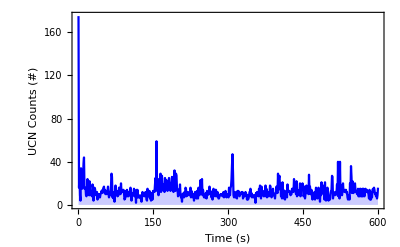

Number of Cycles: 696.

```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum=11369];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadata=ReadList[StringJoin[AscDir,"/",IntegerString[runNum,10,6],"/",IntegerString[runNum,10,6],"_Meta3.edm"],metaStructure2];
EDAListPlot[metadata[[1;;600,32]],PlotStyle->{Blue,Red,Gray},Joined->True,Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","UCN Counts (#)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]
Print["Number of Cycles: ",maxCy=metadata[[-1]][[2]]];
```

```mathematica
Clear[data,histdata2]
data={};
For[runi=1,runi<=maxCy,runi++,
If[runi≠ 11&&runi≠ 46&&runi≠ 117&&runi≠ 165&&runi≠ 188&&runi≠400&&runi≠420,
data=Join[data,ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[runi,10,3],"_0001.fast.ascii"],metaStructure]];
];
];
dimdata=Dimensions[data][[1]]
Dimensions[data]
```

149638

{149638,7}

## Studying timing difference between events

```mathematica
tmdiff=(data[[2;;dimdata,4]]-data[[1;;dimdata-1,4]]);
Dimensions[tmdiff][[1]]
histbeg2=1000;histlast2=2000001000;binw2=100000;
hst2=HistogramList[tmdiff,{histbeg2,histlast2,binw2}];
Total[hst2[[2]]]
histbeg=1;histlast=1001;binw=1;
hst=HistogramList[tmdiff,{histbeg,histlast,binw}];
Total[hst[[2]]]
pt1=ListLinePlot[Transpose[{Log10[hst[[1]][[1;;(histlast-histbeg)/binw]]],hst[[2]]}],PlotRange->{{Log10[1],Log10[histlast]},{0,5000}},Frame->True,PlotRange->Full,FrameLabel->{"Log[ΔTime (ns)]","#Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}];
pt2=ListLinePlot[Transpose[{Log10[hst2[[1]][[1;;(histlast2-histbeg2)/binw2]]],hst2[[2]]}],PlotRange->{{Log10[histbeg2],Log10[histlast2]},{0,100}},Frame->True,PlotRange->Full,FrameLabel->{"Log[ΔTime (ns)]","#Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}];
Export["01_timeStructure.png",GraphicsGrid[{{pt1,pt2}}]]
```

149637

126788

14502

Export::infer: Cannot infer format of file "01_timeStructure".

$Failed

```mathematica
ListLinePlot[Transpose[{hst[[1]][[1;;(histlast2-histbeg2)/binw2]],hst[[2]]}],PlotRange->{{histbeg2,binw2*10},{0,Max[hst[[2]]]}}]
```

```mathematica
Print["# of burst events: ",Dimensions[DeleteCases[cnt,0]][[1]]];
cleandata=Select[data[[1;;dimdata,{3,4,6,5,7}]],(#[[3]]-#[[4]])>145&];
Print["# of clean events: ",Dimensions[cleandata][[1]]];
Print["# of all events: ",Dimensions[data][[1]]];
Print["# Difference: ",Dimensions[data][[1]]-Dimensions[cleandata][[1]]];
Mean[data[[;;,6]]-data[[;;,5]]]
Max[data[[;;,6]]-data[[;;,5]]]
Min[data[[;;,6]]-data[[;;,5]]]
StandardDeviation[data[[;;,6]]-data[[;;,5]]]
```